Negative integrator limit:

```mathematica
soln=Solve[(R2 Vn+R1 Vout)/(R1+R2)==-0.6,Vout]//FullSimplify
```

{{Vout→-0.6+(R2 (-0.6-1. Vn))/R1}}

```mathematica
soln/.{R1->10000,R2->3000,Vn->-10}
```

{{Vout→2.22}}

```mathematica
%[[1,1,2]]
```

2.22

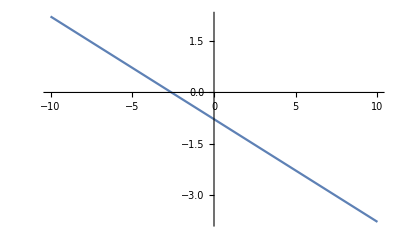

```mathematica
Plot[(soln/.{R1->10000,R2->3000})⟦1,1,2⟧,{Vn,-10,10}]
```

Positive integrator limit:

```mathematica
soln=Solve[(R3 Vp+R4 Vout)/(R3+R4)==0.6,Vout]//FullSimplify
```

{{Vout→0.6+(R3 (0.6-1. Vp))/R4}}

```mathematica
soln/.{R4->10000,R3->3000,Vp->10}
```

{{Vout→-2.22}}

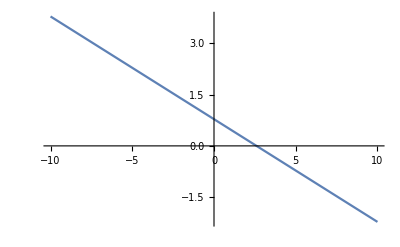

```mathematica
Plot[(soln/.{R4->10000,R3->3000})⟦1,1,2⟧,{Vp,-10,10}]
```